```mathematica
points= {{-1,3},{0,0.5},{0.5,0},{1,1}};

langrangePoly = InterpolatingPolynomial[points, x]
```

3+(1+x) (-1+(-1+x) (1.5+1. x))

```mathematica
f25 = langrangePoly /. x -> 0.25
```

0.109375

```mathematica
f75 = langrangePoly /. x-> 0/75
```

0.5

```mathematica
points = {{-1, 1.5},{0,0},{0.5,0},{1,0.5}};
langrangePoly = InterpolatingPolynomial[points, x];
f25 = langrangePoly /. x-> -0.25;
f25' = langrangePoly /. x-> 0.25;
{langrangePoly, f25, f25'}
```

{1.5+(-0.5+1. (-1+x)) (1+x),0.1875,-0.0625}

```mathematica
?Fit
```

2.07897+2.09235 x

1.94449+2.0851 x+0.28191 x^2

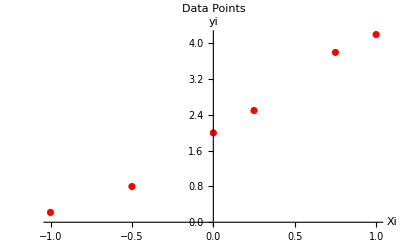

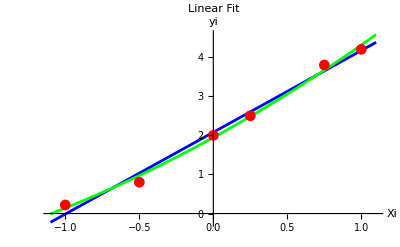

```mathematica
data={{-1.00,0.22},{-0.50,0.80},{0,2.0},{0.25,2.5},{0.75,3.8},{1.00,4.2}};

linearFit=Fit[data,{1,x},x]

quadraticFit=Fit[data,{1,x,x^2},x]

ListPlot[data,PlotStyle->Red,PlotLabel->"Data Points",AxesLabel->{"Xi","yi"},PlotRange->All]
Show[Plot[linearFit,{x,-1.1,1.1},PlotStyle->Blue,PlotLabel->"Linear Fit"],Plot[quadraticFit,{x,-1.1,1.1},PlotStyle->Green,PlotLabel->"Quadratic Fit"],ListPlot[data,PlotStyle->Red,PlotMarkers->Automatic],PlotRange->All,AxesLabel->{"Xi","yi"}]
```

```mathematica
points = {{19,19.00},{23,28.50},{30,47.00},{35,68.20},{40,90.00}};
fit = Fit[points, {1,x^2},x]
```

-2.37227+0.0573264 x^2

```mathematica
points={{0,2.00},{1,2.50},{2,4.00},{3,6.00},{4,8.00}};

fitParams=FindFit[points,a*Exp[b*x],{a,b},x]
fit=a*Exp[b*x]/. fitParams
```

{a→1.94454,b→0.358018}

1.94454 ⅇ^(0.358018 x)

```mathematica
c= {-3,-2};
m = {{1,-2},{-3,-2},{-1,1}};
b= {-4,-14, -3};
l = {0,0};
solution = LinearProgramming[c, m , b]
```

{4,1}

```mathematica
c= {2,3,4};
delta = 10^-5;
m = {{-1,-2,1},{-1,-1,1},{0,-1,-2}};
b = {10+delta, 60, 12+delta};
solution = LinearProgramming[c, -m,b,{delta,delta,1+delta}]
```

{2550001/50000,999999/100000,100001/100000}

```mathematica
(*We make some modifications:
z' = z - 1, then z' > 0
min m = 2x+3y+4z'+4
x = Subscript[x, 1]-Subscript[x, 2], y = Subscript[y, 1]-Subscript[y, 2], z' = Subscript[z, 1]-Subscript[z, 2]*)
c= {2, -2, 3, -3, 4, -4,0,0};
m = {{1,-1,2,-2,-1,1,-1,0},{1,-1,1,-1,-1,1,0,0},{0,0,1,-1,2,-2,0,-1}};
b= {11,61,10};
solution = LinearProgramming[c, m, b]
```

LinearProgramming::lpsub: 该问题是无界的.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

{{y[x]→1/4 (-2 Cos[x]+2 Cos[x]^3+2 x Sin[x]+Sin[x] Sin[2 x])}}

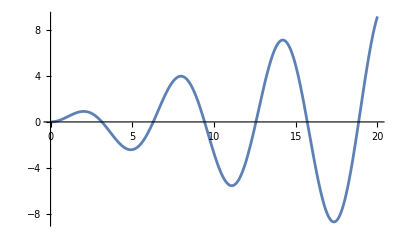

```mathematica
DSolve[{y''[x]+y[x]==Cos[x],y[0]==0,y'[0]==0},y[x],x]
sol=y[x]/. First[%];
Plot[sol,{x,0,20}]
```

```mathematica
Clear["Global`*"]
solution = NDSolve[{u'[t] == 0.09*u[t]*(1-u[t]/20)-0.45*u[t]*v[t],v'[t] == 0.06*v[t]*(1-v[t]/15)-0.001*u[t]*v[t],u[0]==1.6,v[0]==1.2},{u,v},{t,20}]

Plot[Evaluate[{u[t],v[t]}/. solution],{t,0,20},PlotLabels->{"u(t)","v(t)"},PlotLegends->Placed[{"u(t)","v(t)"},Above],PlotStyle->{Blue,Red}]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

-Graphics-

```mathematica
heatEquation=D[u[x,t],t]==D[u[x,t],{x,2}];

initialCondition=u[x,0]==0;


boundaryConditions={u[0,t]==Sin[t],u[5,t]==0};


solution=NDSolve[{heatEquation,initialCondition,boundaryConditions},u,{x,0,5},{t,0,10}];


Plot3D[Evaluate[u[x,t]/. solution],{x,0,5},{t,0,10},PlotLabel->"Temperature Distribution",AxesLabel->{"x","t","u(x, t)"},Mesh->None,PlotStyle->Directive[Opacity[0.7],Blue]]
```

-Graphics3D-

```mathematica
ClearAll[u,x,t]

(*定义波动方程*)len=10;  (*定义计算区域的长度*)
pde=D[u[x,t],{t,2}]==D[u[x,t],{x,2}];

(*设置初始条件*)
ic={u[x,0]==Exp[-x^2],Derivative[0,1][u][x,0]==0}; (*初始位移和速度*)

(*设置边界条件：周期性边界条件*)
bc={u[-len,t]==u[len,t],Derivative[1,0][u][-len,t]==Derivative[1,0][u][len,t]};

(*使用 NDSolve 求解波动方程*)
solution=NDSolve[{pde,ic[[1]],ic[[2]],bc[[1]],bc[[2]]},u,{x,-len,len},{t,0,40}]
```

{{u→InterpolatingFunction[{{…, -10., 10., …}, {0., 40.}}, <>]}}

```mathematica
(*可视化解*)uSolution[x_,t_]:=u[x,t]/. solution[[1]];
Plot3D[uSolution[x,t],{x,-len,len},{t,0,40},PlotRange->All,AxesLabel->{"x","t","u(x, t)"},MeshFunctions->{#3&},Mesh->10]
```

-Graphics3D-